ruleResults not found in memory. Importing summary CSV instead...

ToExpression::sntxi: Incomplete expression; more input is needed.

General::stop: Further output of ToExpression::sntxi will be suppressed during this calculation.

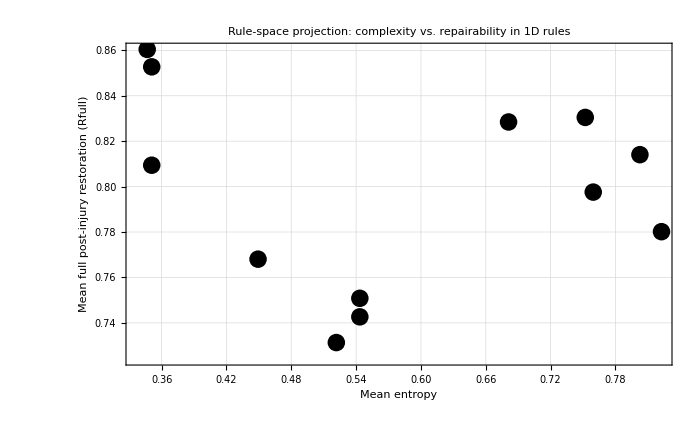

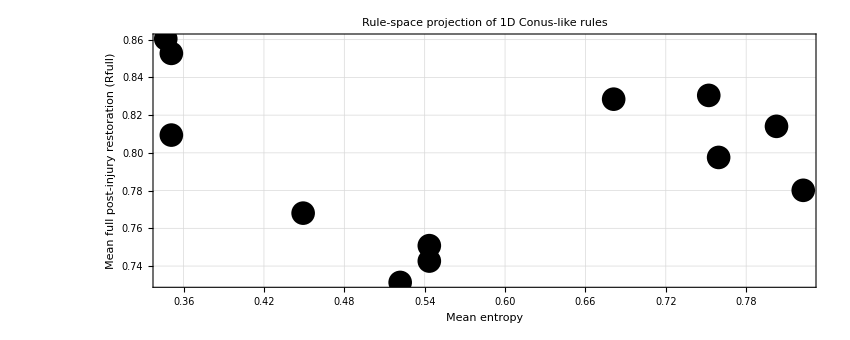

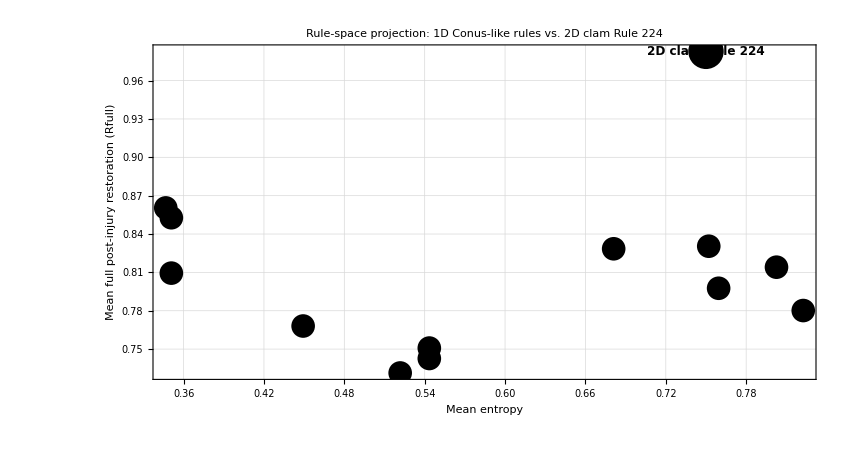

Exports saved to: /Volumes/External/Ruliology/rule_space_projection_exports

```mathematica
ClearAll["Global`*"];

(* =========================================================1. Ensure paths and data exist=========================================================*)

(*Set export directory explicitly*)
exportBase=FileNameJoin[{NotebookDirectory[],"rule_space_projection_exports"}];
If[!DirectoryQ[exportBase],CreateDirectory[exportBase]];

(*If ruleResults is not already in memory,import from CSV*)
If[!ValueQ[ruleResults],Print["ruleResults not found in memory. Importing summary CSV instead..."];
summaryCSV=FileNameJoin[{NotebookDirectory[],"conus_repeated_trials_exports","conus_repeated_trials_summary.csv"}];
If[FileExistsQ[summaryCSV],imported=Import[summaryCSV];
headers=First[imported];
rows=Rest[imported];
ruleResults=Map[AssociationThread[headers,#]&,rows];
(*Convert numeric columns from strings if needed*)ruleResults=ruleResults/. a_Association:>Association[a,"Rule"->ToExpression[a["Rule"]],"MeanFinalR"->ToExpression[a["MeanFinalR"]],"SDFinalR"->ToExpression[a["SDFinalR"]],"MeanFullR"->ToExpression[a["MeanFullR"]],"SDFullR"->ToExpression[a["SDFullR"]],"Density"->ToExpression[a["Density"]],"Entropy"->ToExpression[a["Entropy"]],"Variation"->ToExpression[a["Variation"]]];,Print["Could not find summary CSV. Please either run the repeated-trial notebook first or set summaryCSV correctly."];
Abort[]]];

(* =========================================================2. Normalize field names=========================================================*)

(*Support either old-style or new-style keys*)
normalizedRuleResults=ruleResults/. a_Association:><|"Rule"->Lookup[a,"Rule"],"Entropy"->Lookup[a,"Entropy"],"MeanRfull"->Lookup[a,"MeanRfull",Lookup[a,"MeanFullR"]],"Variation"->Lookup[a,"Variation"],"Class"->Lookup[a,"Class","Unclassified"]|>;

(*Remove bad/missing rows*)
normalizedRuleResults=Select[normalizedRuleResults,NumericQ[#["Entropy"]]&&NumericQ[#["MeanRfull"]]&];

If[Length[normalizedRuleResults]==0,Print["No valid rows found after normalization."];
Abort[]];

(* =========================================================3. Rule-space data=========================================================*)

ruleSpaceData=normalizedRuleResults;

(* =========================================================4. Simple plot=========================================================*)

ruleSpacePlot=ListPlot[ruleSpaceData/. a_Association:>{a["Entropy"],a["MeanRfull"]},Frame->True,Axes->False,FrameLabel->{Style["Mean entropy",14],Style["Mean full post-injury restoration (Rfull)",14]},PlotStyle->Directive[Black,PointSize[0.018]],PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],PlotLabel->Style["Rule-space projection: complexity vs. repairability in 1D rules",15,Bold],ImageSize->700];

ruleSpacePlot

(* =========================================================5. Classified plot=========================================================*)

classColor[class_]:=Switch[class,"Trivial sparse",Gray,"Trivial full",Darker[Gray],"Simple periodic",Blue,"Chaotic fragile",Red,"Structured robust",Darker[Green],"Fractal / nested",Purple,"Mixed / intermediate",Orange,_,Black];

classifiedPoints=ruleSpaceData/. a_Association:>{classColor[a["Class"]],PointSize[0.02],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],9],{a["Entropy"],a["MeanRfull"]},{0,-1.2}]};

ruleSpaceClassPlot=Graphics[classifiedPoints,Frame->True,Axes->False,FrameLabel->{Style["Mean entropy",14],Style["Mean full post-injury restoration (Rfull)",14]},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],ImageSize->850,PlotLabel->Style["Rule-space projection of 1D Conus-like rules",15,Bold]];

ruleSpaceClassPlot

(* =========================================================6. Add 2D clam point=========================================================*)

(*Use manual clam point for now unless you load a real 2D array*)
clamEntropy=0.75;   (*replace later if computed*)
clamRfull=0.9829;

ruleSpaceWithClam=Show[ruleSpaceClassPlot,Graphics[{{Black,PointSize[0.03],Point[{clamEntropy,clamRfull}]},Text[Style["2D clam Rule 224",12,Bold,Background->White],{clamEntropy,clamRfull},{0,-1.2}]}],PlotLabel->Style["Rule-space projection: 1D Conus-like rules vs. 2D clam Rule 224",15,Bold]];

ruleSpaceWithClam

(* =========================================================7. Export=========================================================*)

Export[FileNameJoin[{exportBase,"rule_space_projection.png"}],ruleSpaceWithClam,ImageResolution->300];

Export[FileNameJoin[{exportBase,"rule_space_projection.pdf"}],ruleSpaceWithClam];

Print["Exports saved to: ",exportBase];
```

```mathematica
labelOffset={0.005,0.002};

cleanPoints=ruleSpaceData/. a_Association:>{Black,PointSize[0.02],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],10],{a["Entropy"],a["MeanRfull"]}+labelOffset]};
```

```mathematica
classColor[class_]:=Switch[class,"Simple periodic",Blue,"Chaotic fragile",Red,"Structured robust",Darker[Green],"Fractal / nested",Purple,"Mixed / intermediate",Orange,_,Gray];
```

```mathematica
coloredPoints=ruleSpaceData/. a_Association:>{classColor[a["Class"]],PointSize[0.022],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],10],{a["Entropy"],a["MeanRfull"]}+{0.005,0.002}]};
```

```mathematica
topRules={18,60,110};

highlightedPoints=ruleSpaceData/. a_Association:>{If[MemberQ[topRules,a["Rule"]],Red,classColor[a["Class"]]],If[MemberQ[topRules,a["Rule"]],PointSize[0.035],PointSize[0.02]],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],11,Bold],{a["Entropy"],a["MeanRfull"]}+{0.006,0.003}]};
```

```mathematica
clamEntropy=0.75;   (*replace later if computed*)
clamRfull=0.983;

clamPoint={Black,PointSize[0.045],Point[{clamEntropy,clamRfull}],Text[Style["2D clam (Rule 224)",12,Bold,Background->White],{clamEntropy,clamRfull},{0,-1.5}]};
```

```mathematica
clamEntropy=0.75;   (*replace later if computed*)
clamRfull=0.983;

clamPoint={Black,PointSize[0.045],Point[{clamEntropy,clamRfull}],Text[Style["2D clam (Rule 224)",12,Bold,Background->White],{clamEntropy,clamRfull},{0,-1.5}]};
```

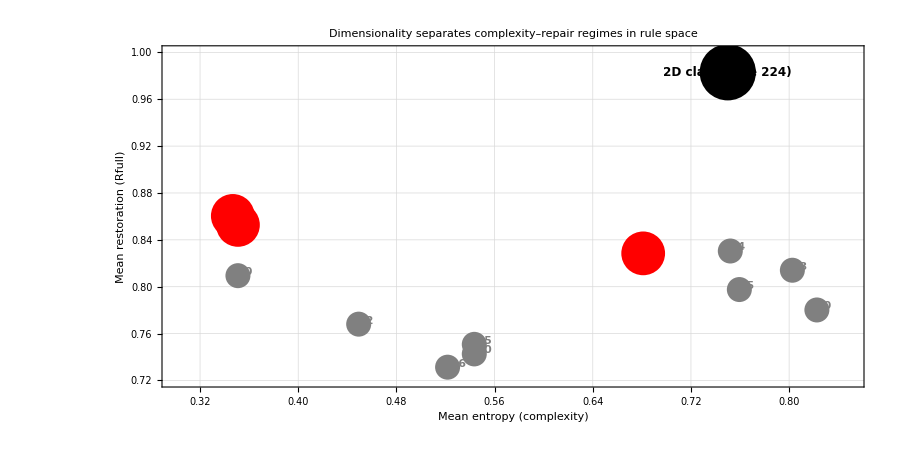

```mathematica
finalPlot=Graphics[{highlightedPoints,clamPoint},Frame->True,Axes->False,FrameLabel->{Style["Mean entropy (complexity)",15],Style["Mean restoration (Rfull)",15]},PlotRange->{{0.3,0.85},{0.72,1.0}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9]],ImageSize->900,PlotLabel->Style["Dimensionality separates complexity–repair regimes in rule space",16,Bold]];

finalPlot
```

```mathematica
ClearAll["Global`*"];

(*---------------------------------------------------------Example data structure assumed:ruleSpaceData=list of associations with keys:"Rule","Entropy","MeanRfull","Class"---------------------------------------------------------*)

(*Top highlighted 1D rules*)
topRules={18,60,110,30};

(*Manual clam point*)
clamEntropy=0.75;
clamRfull=0.9829;

(*Colors*)
classColor[class_]:=Switch[class,"Simple periodic",RGBColor[0.4,0.55,0.9],"Chaotic fragile",RGBColor[0.85,0.45,0.45],"Structured robust",GrayLevel[0.55],"Fractal / nested",RGBColor[0.7,0.5,0.85],"Mixed / intermediate",GrayLevel[0.7],"Trivial sparse",GrayLevel[0.85],"Trivial full",GrayLevel[0.85],_,GrayLevel[0.7]];

(*Extract numeric coordinates*)
pts1D=ruleSpaceData/. a_Association:>{a["Entropy"],a["MeanRfull"]};

(*Best 1D restoration value*)
best1DR=Max[ruleSpaceData[[All,"MeanRfull"]]];

(*Bounding rectangle for 1D cloud*)
xmin=Min[pts1D[[All,1]]]-0.01;
xmax=Max[pts1D[[All,1]]]+0.01;
ymin=Min[pts1D[[All,2]]]-0.01;
ymax=Max[pts1D[[All,2]]]+0.01;

(*Build graphics primitives*)
backgroundRegion={Directive[GrayLevel[0.92],Opacity[0.35]],Rectangle[{xmin,ymin},{xmax,ymax}]};

allPoints=ruleSpaceData/. a_Association:>{classColor[a["Class"]],PointSize[0.022],Point[{a["Entropy"],a["MeanRfull"]}]};

topPointLabels=ruleSpaceData/. a_Association:>If[MemberQ[topRules,a["Rule"]],{Red,PointSize[0.03],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],12,Bold,Background->White],{a["Entropy"],a["MeanRfull"]}+{0.006,0.003}]},Nothing];

best1DLine={Directive[Black,Dashed,Thickness[0.002]],Line[{{0.3,best1DR},{0.85,best1DR}}],Text[Style["best 1D restoration",11,Background->White],{0.62,best1DR+0.003}]};

oneDLabel={Text[Style["1D shell-like rule regime\n(complexity–repair tradeoff)",13,Bold,Background->White],{0.47,0.865}]};

dimensionalityArrow={Directive[Black,Thick,Arrowheads[0.03]],Arrow[{{0.69,0.845},{clamEntropy-0.01,clamRfull-0.01}}],Text[Style["dimensionality gain:\n2D escapes the 1D tradeoff",12,Bold,Background->White],{0.69,0.93}]};

clamPoint={Black,PointSize[0.038],Point[{clamEntropy,clamRfull}],Text[Style["2D clam\nRule 224",13,Bold,Background->White],{clamEntropy,clamRfull}+{0.005,0.005}]};

finalPlot=Graphics[{backgroundRegion,allPoints,topPointLabels,best1DLine,oneDLabel,dimensionalityArrow,clamPoint},Frame->True,Axes->False,FrameLabel->{Style["Mean entropy (complexity)",16],Style["Mean post-injury restoration (Rfull)",16]},PlotRange->{{0.3,0.85},{0.72,1.0}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.88]],ImageSize->950,PlotLabel->Style["Dimensionality separates complexity–repair regimes in rule space",18,Bold],BaseStyle->{FontFamily->"Helvetica"}];

finalPlot
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Attributes::ssle: Symbol or string expected at position 1 in Attributes[Symbol[]].

-Graphics-